```mathematica
Subscript[ϕ, 0][s_,t_]=1-s-t; Subscript[ϕ, 1][s_,t_]=s; Subscript[ϕ, 2][s_,t_]=t;
```

```mathematica
triRefInt[f_]:=Integrate[f, {s,0,1},{t,0,1-s}]
```

```mathematica
refMass = Table[triRefInt[Subscript[ϕ, i][s,t]Subscript[ϕ, j][s,t]],{i,0,2},{j,0,2}]
```

(1/12 | 1/24 | 1/24
1/24 | 1/12 | 1/24
1/24 | 1/24 | 1/12)

```mathematica
grad[f_]:={D[f,s],D[f,t]}
```

```mathematica
refLapl = Table[triRefInt[grad[Subscript[ϕ, i][s,t]].grad[Subscript[ϕ, j][s,t]]],{i,0,2},{j,0,2}]
```

(1 | -1/2 | -1/2
-1/2 | 1/2 | 0
-1/2 | 0 | 1/2)

```mathematica
JJ={{Subscript[J, x,s],Subscript[J, x,t]},{Subscript[J, y,s],Subscript[J, y,t]}}
```

(J_(x,s) | J_(x,t)
J_(y,s) | J_(y,t))

```mathematica
Det[JJ]
```

J_(x,s) J_(y,t)-J_(y,s) J_(x,t)

```mathematica
Inverse[JJ].Inverse[Transpose[JJ]]//FullSimplify
```

((J_(x,t)^2+J_(y,t)^2)/(J_(y,s) J_(x,t)-J_(x,s) J_(y,t))^2 | -(J_(x,s) J_(x,t)+J_(y,s) J_(y,t))/(J_(y,s) J_(x,t)-J_(x,s) J_(y,t))^2
-(J_(x,s) J_(x,t)+J_(y,s) J_(y,t))/(J_(y,s) J_(x,t)-J_(x,s) J_(y,t))^2 | (J_(x,s)^2+J_(y,s)^2)/(J_(y,s) J_(x,t)-J_(x,s) J_(y,t))^2)

```mathematica
Cos[11Pi/6]
```

(√3)/2

```mathematica
x
```

x

```mathematica
AA = {Cos[7Pi/6], Sin[7Pi/6]}; BB={Cos[11Pi/6],Sin[11Pi/6]}; CC={Cos[Pi/2], Sin[Pi/2]};
```

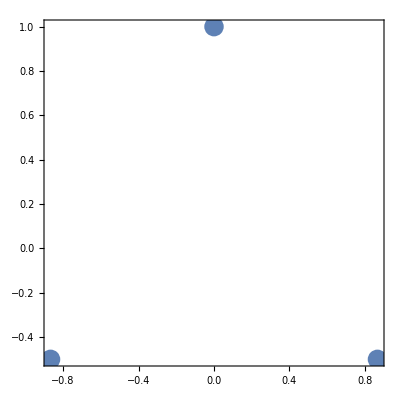

```mathematica
nodes=ListPlot[{AA,BB,CC},AspectRatio->1,PlotMarkers->{Automatic,Large}]
```

```mathematica
y1[x_]=AA[[2]] + (CC[[2]]-AA[[2]])(x-AA[[1]])/(CC[[1]]-AA[[1]])
```

√3 (x+(√3)/2)-1/2

```mathematica
y2[x_]=CC[[2]] + (BB[[2]]-CC[[2]])(x-CC[[1]])/(BB[[1]]-CC[[1]])
```

1-√3 x

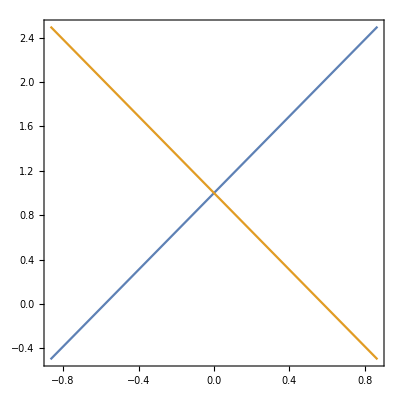

```mathematica
lines=Plot[{y1[x],y2[x]},{x,AA[[1]],BB[[1]]},AspectRatio->1]
```

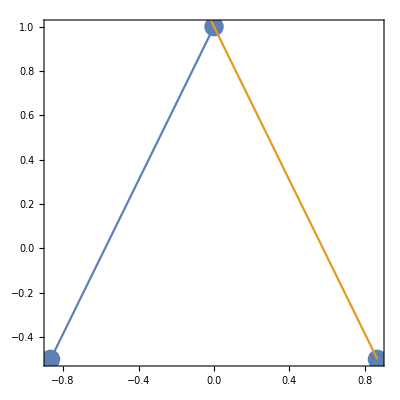

```mathematica
Show[nodes, lines]
```

```mathematica
triEqInt[f_]:=Integrate[f,{x,AA[[1]],0},{y,AA[[2]],y1[x]}]+Integrate[f,{x,0, BB[[1]]},{y,AA[[2]],y2[x]}]
```

```mathematica
triEqInt[1]//FullSimplify
```

(3 √3)/4

```mathematica
Subscript[p, 2][x_,y_]=Subscript[c, 0]+Subscript[c, 1] x + Subscript[c, 2] y+Subscript[c, 3] x^2+Subscript[c, 4] y^2+Subscript[c, 5] x y
```

c_3 x^2+c_5 x y+c_1 x+c_4 y^2+c_2 y+c_0

```mathematica
triEqInt[Subscript[p, 2][x,y]]//FullSimplify
```

3/32 √3 (8 c_0+c_3+c_4)

```mathematica
Subscript[θ, i_]=Pi/2+(i-1)2Pi/3
```

2/3 π (i-1)+π/2

```mathematica
Table[Subscript[θ, i],{i,1,3}]
```

{π/2,(7 π)/6,(11 π)/6}

```mathematica
Q[f_]:=w Sum[f[ρ Cos[Subscript[θ, i]],ρ Sin[Subscript[θ, i]]],{i,1,3}]
```

```mathematica
Q[g]
```

w (g(0,ρ)+g(-(√3 ρ)/2,-ρ/2)+g((√3 ρ)/2,-ρ/2))

```mathematica
Q[Subscript[p, 2]]
```

w ((3 c_3 ρ^2)/2+(3 c_4 ρ^2)/2+3 c_0)

```mathematica
eqns = Table[
Coefficient[FullSimplify[triEqInt[Subscript[p, 2][x,y]]],Subscript[c, j]]==
Coefficient[Q[Subscript[p, 2]],Subscript[c, j]],{j,{0,3,4}}]
```

{(3 √3)/4==3 w,(3 √3)/32==(3 ρ^2 w)/2,(3 √3)/32==(3 ρ^2 w)/2}

```mathematica
Solve[eqns, {w,ρ}]
```

{{w→(√3)/4,ρ→-1/2},{w→(√3)/4,ρ→1/2}}

```mathematica
quadPoints[ρ_]:=ListPlot[Table[{ρ Cos[Subscript[θ, i]],ρ Sin[Subscript[θ, i]]},{i,1,3}],AspectRatio->1,PlotMarkers->{Automatic,Medium}]
```

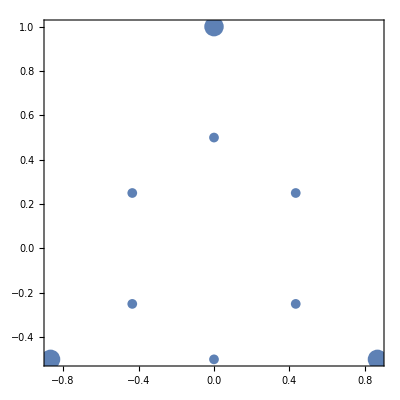

```mathematica
Show[nodes, quadPoints[1/2],quadPoints[-1/2]]
```